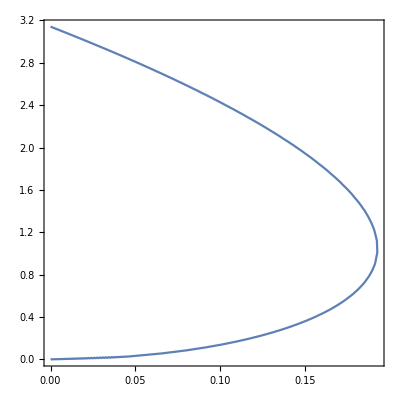

```mathematica
(* Schwarzschild-DeSitter enetropy using contour plot *)

ContourPlot[0== (S/π)^(1/2)- 2M-( S/π)^(3/2),{M,0, √(1/27)},{S,0,π}]
```

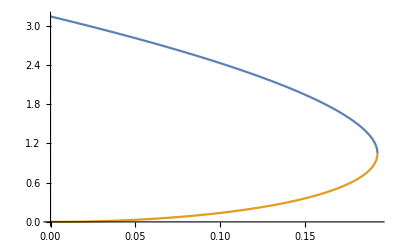

```mathematica
(* Schwarschils DeSitte using (17) and (18) from https://arxiv.org/pdf/gr-qc/0301090.pdf *)

Plot[{π((2M)/(√(3(M^2/1)))Cos[1/3(π- ArcCos[3 √(3 M^2/1)])])^2,π((2M)/(√(3(M^2/1)))Cos[1/3(π+ ArcCos[3 √(3 M^2/1)])])^2},{M,0, √(1/27)},PlotRange->{0,π}]
```

```mathematica
(* These methods agree blue is entropy Cosmological horizon and orange entropy of black hole horizon, the right hand point where they meet id the Narai spacetime *)
```

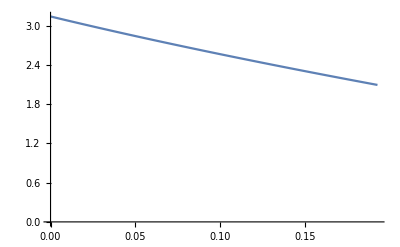

```mathematica
(* Adding the two entropies yeilds *)


Plot[π((2M)/(√(3(M^2/1)))Cos[1/3(π- ArcCos[3 √(3 M^2/1)])])^2+π((2M)/(√(3(M^2/1)))Cos[1/3(π+ ArcCos[3 √(3 M^2/1)])])^2,{M,0, √(1/27)},PlotRange->{0,π}]
```

```mathematica
(* Narai spacetime has less entropy 2 pi/3 then Desitter whicj is pi. Entropy should increase so Narai may be unstable *)


(* for small black hole M << l we have the expansions *)
```

```mathematica
Simplify[Series[π((2 l)/(√(3(1/1)))Cos[1/3(π- ArcCos[3 M/l √(3 1/1)])])^2,{M,0,4}]]
```

l^2 π-2 (l π) M-2 π M^2-(5 π M^3)/l-(16 π M^4)/l^2+O[M]^5

```mathematica
Simplify[Series[π((2 l)/(√(3(1/1)))Cos[1/3(π+ ArcCos[3 M/l √(3 1/1)])])^2,{M,0,4}]]
```

4 π M^2+(32 π M^4)/l^2+O[M]^5

```mathematica
(* Black holes cause DeSitter cosmological entropy to decrease *)

(* cosmological constant cause blackhole enetropy to increase faster with mass *)
```

```mathematica
(* Now let's compute the temperature of DeSitter and Schwarzschild-DeSitter black hole using beta = T^^{-1} = partial S/ partial M *)
```

```mathematica
D[(π((2M)/(√(3(M^2/1)))Cos[1/3(π+ ArcCos[3 √(3 M^2/1)])])^2), M]
```

(8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2))

```mathematica
D[(π((2M)/(√(3(M^2/1)))Cos[1/3(π- ArcCos[3 √(3 M^2/1)])])^2), M]
```

-(8 M π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2))

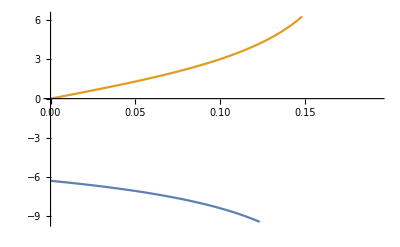

```mathematica
Plot[{-(8 M π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)),(8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2))},{M,0, √(1/27)},PlotRange->{-3π,2π}]
```

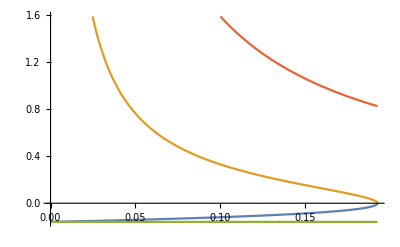

```mathematica
Plot[{-((8 M π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)))^-1,((8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)))^-1,-1/(2π), 1/(2π M)},{M,0, √(1/27)},PlotRange->{-(2π)^-1,(.2π)^-1}]
```

```mathematica
(* This indicates Narai spacetime is unstable with zero temperature and DeSitter has temperature -1/(2 pi) *)
```

```mathematica
Series[(8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)),{M,0,8}]
```

8 π M+128 π M^3+2688 π M^5+61440 π M^7+O[M]^9

```mathematica
Series[((8 M π Cos[1/3 (π+ArcCos[3 √3 √(M^2)])] Sin[1/3 (π+ArcCos[3 √3 √(M^2)])])/(√3 √(M^2) √(1-27 M^2)))^-1,{M,0,8}]
```

1/(8 π M)-(2 M)/π+(√3 (-32/(√3)-16 √3) M^3)/(8 π)+(√3 (-448/(√3)-192 √3) M^5)/(8 π)-(2112 M^7)/π+O[M]^9

```mathematica
Series[-((8 π Cos[1/3 (π-ArcCos[3 √3 √(M^2)])] Sin[1/3 (π-ArcCos[3 √3 √(M^2)])])/(√3  √(1-27 M^2)))^-1,{M,0,8}]
```

-1/(2 π)+(√(M^2) M)/(M π)+(7 M^2)/(4 π)+(5 √(M^2) M^3)/(M π)+(273 M^4)/(16 π)+(64 √(M^2) M^5)/(M π)+(8151 M^6)/(32 π)+(1056 √(M^2) M^7)/(M π)+(1154725 M^8)/(256 π)+O[M]^9

```mathematica
(* The black hole makes the DeSitter temperature decrease in absolute value. The cosmological constant make the the blackhole temperature decrease.
```